# 公式区域投影

公式区域表示一个 ℝ^3 中的立体

```mathematica
ℛ=ImplicitRegion[x^6-5 x^4 y z+3 x^4 y^2+10 x^2 y^3 z+3 x^2 y^4-y^5 z+y^6+z^6<=1,{x,y,z}];
```

可视化区域

```mathematica
RegionPlot3D[ℛ,PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.6,1.6}},PlotPoints->50]
```

-Graphics3D-

求坐标平面上ℝ的投影

Resolve::ratnz: Resolve 无法从具有不精确系数的系统中消去量词. 通过从相应的精确系统消去量词，并且将结果数值化处理，获取答案.

General::stop: 在本次计算中，Resolve::ratnz 的进一步输出将被抑制.

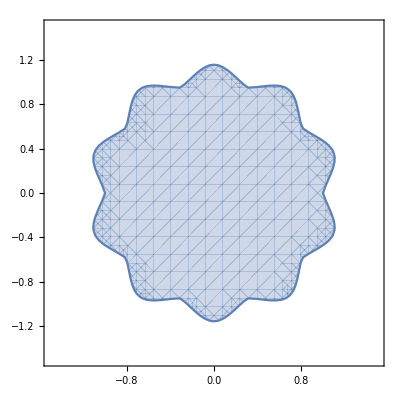
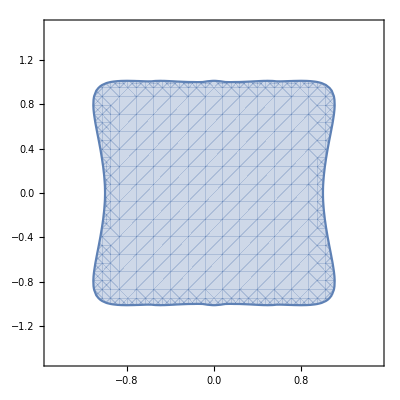
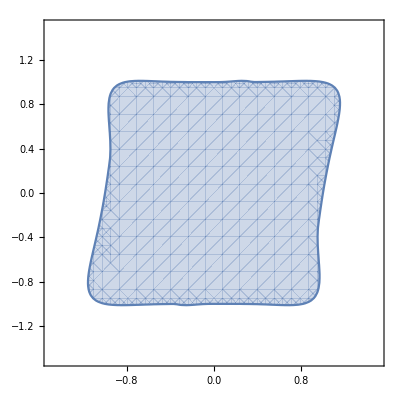

```mathematica
{RegionPlot[Resolve[∃_z{x,y,z}∈ℛ, Reals], {x, -1.5, 
   1.5}, {y, -1.5, 1.5}], RegionPlot[Resolve[∃_y{x,y,z}∈ℛ, Reals], {x, -1.5, 
   1.5}, {z, -1.5, 1.5}], RegionPlot[Resolve[∃_x{x,y,z}∈ℛ, Reals], {y, -1.5, 
   1.5}, {z, -1.5, 1.5}]}
```